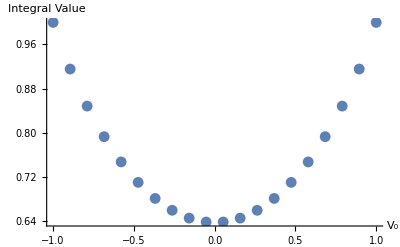

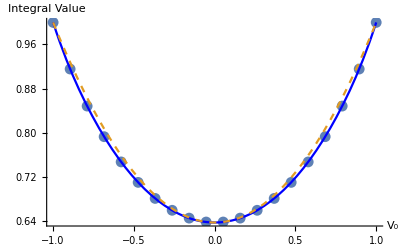

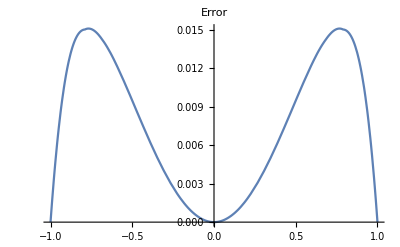

```mathematica
(* Quadratic Approximation *)
f[A_,V_]:=1/(2π)∫_0^(2π) Abs[-A Cos[x]+V]ⅆx
Data[A_,n_]:=Table[f[A,V],{V,-A,A,(2A)/(n-1)}]
Vpoints[A_,n_]:=Table[V,{V,-A,A,(2A)/(n-1)}]
quadraticapprox[A_,x_]:=(2Abs[A])/π+1/Abs[A](1-2/π)x^2
Clear[A,n,yval,xval,points,g,p1,p2,p3]
A=1.;
n=20*Ceiling[A];
xval=Vpoints[A,n];
yval=Data[A,n];
points=Partition[Riffle[xval,yval],2];
g=Interpolation[points];
p1=ListPlot[points,AxesLabel->{"V_0","Integral Value"}]
p2=Plot[{g[x],quadraticapprox[A,x]},{x,-A,A},PlotStyle->{Blue,Dashed}];
Show[p1,p2]
p3=Plot[Abs[g[x]-quadraticapprox[A,x]],{x,-A,A},PlotLabel->"Error"]
```

```mathematica
Directory[]
SetDirectory["C:\\Users\\codyg_000\\Desktop\\MSC_Thesis"]
```

C:\Users\codyg_000\Desktop\MSC_Thesis

C:\Users\codyg_000\Desktop\MSC_Thesis

```mathematica
Export["datapoints.jpg",p1]
Export["quadratic_comparison.jpg",p2]
Export["quadratic_error.jpg",p3]
```

datapoints.jpg

quadratic_comparison.jpg

quadratic_error.jpg

-Graphics-

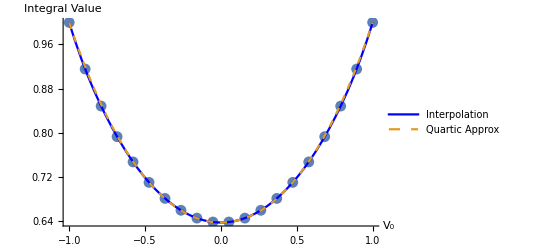

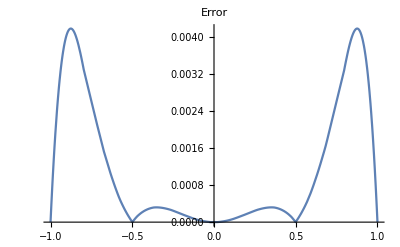

```mathematica
(* Quartic Approximation *)
f[A_,V_]:=1/(2π)∫_0^(2π) Abs[-A Cos[x]+V]ⅆx
Data[A_,n_]:=Table[f[A,V],{V,-A,A,(2A)/(n-1)}]
Vpoints[A_,n_]:=Table[V,{V,-A,A,(2A)/(n-1)}]
quarticapprox[A_,x_]:=(2Abs[A])/π+1/(3Abs[A])(16(1/6+(√3)/π)-15(2/π)-1)x^2-4/(3 Abs[A]^3)(4(1/6+(√3)/π)-3(2/π)-1)x^4
Clear[A,n,yval,xval,points,g,p1,p2,p3]
A=1.;
n=20*Ceiling[A];
xval=Vpoints[A,n];
yval=Data[A,n];
points=Partition[Riffle[xval,yval],2];
g=Interpolation[points];
p1=ListPlot[points,AxesLabel->{"V_0","Integral Value"}]
p2=Plot[{g[x],quarticapprox[A,x]},{x,-A,A},PlotStyle->{Blue,Dashed},PlotLegends->{"Interpolation","Quartic Approx"}];
Show[p1,p2]
p3=Plot[Abs[g[x]-quarticapprox[A,x]],{x,-A,A},PlotLabel->"Error"]
```

```mathematica
Directory[]
SetDirectory["C:\\Users\\codyg_000\\Desktop\\MSC_Thesis"]
```

C:\Users\codyg_000\Desktop\MSC_Thesis

C:\Users\codyg_000\Desktop\MSC_Thesis

```mathematica
Export["quartic_comparison.jpg",p2]
Export["quartic_error.jpg",p3]
```

quartic_comparison.jpg

quartic_error.jpg